## Studying the Energy Function in terms of its extreme points

Get the minium and the maximum value for the Energy Function of the triaxial rotor at a given spin.

## Expression of the energy function

```mathematica
IF[X_]:=1/(2*X);
A1=IF[72];
A2=IF[15];
A3=IF[7];
V=2.1;
γ=22*π/180;
j=13/2;
H[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ+π/6];
```

### Experimental data

```mathematica
spin1=Table[8.5+2*i,{i,0,20}];
spin2=Table[13.5+2*i,{i,0,16}];
spin3=Table[16.5+2*i,{i,0,13}];
spin4=Table[23.5+2*i,{i,0,9}];
```

## Find the extremal points

```mathematica
max[spin_]:=FindMaximum[{H[spin,x,y,A1,A2,A3,V,γ],x≥0&&x≤π&&y≥0&&y≤2π},{x,y}][[1]];
min[spin_]:=FindMinimum[{H[spin,x,y,A1,A2,A3,V,γ],x≥0&&x≤π&&y≥0&&y≤2π},{x,y}][[1]];
MINMAX[spin_]:={min[spin],max[spin]};
```

### Customize template

```mathematica
customize[item_]:=Style[item,19,Bold,Black,FontFamily->"Times New Roman"];
```

```mathematica
list={{customize[StringTemplate["V_min"][]],customize[StringTemplate["V_max"][]]}};
procedure[spin_]:=Do[AppendTo[list,{customize[MINMAX[spin[[i]]][[1]]],customize[MINMAX[spin[[i]]][[2]]]}],{i,1,Length[spin]}];
table:=Grid[list,Frame->All,
Background->{None,{LightBlue,{LightGreen}}}];
procedure[spin1]
table
```

V_min | V_max
-1.83422 | 3.31806
-1.64613 | 6.07262
-1.40248 | 9.39861
-1.10327 | 13.296
-0.74851 | 17.7649
-0.338192 | 22.8052
0.127681 | 28.4169
0.64911 | 34.6
1.22609 | 41.3546
1.85863 | 48.6806
2.54673 | 56.578
3.29038 | 65.0468
4.08959 | 74.0871
4.94435 | 83.6988
5.85467 | 93.8819
6.82054 | 104.637
7.84197 | 115.963
8.91895 | 127.86
10.0515 | 140.329
11.2396 | 153.369
12.4832 | 166.981

## Maximum energy for each spin state

```mathematica
lp[band_]:=ListPlot[Table[{band[[i]],MINMAX[band[[i]]][[2]]},{i,1,Length[band]}]];
```

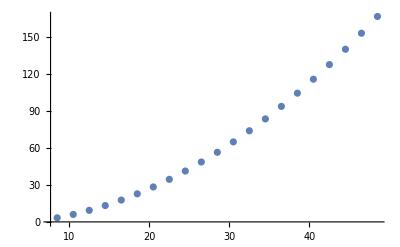

```mathematica
lp[spin1]
```

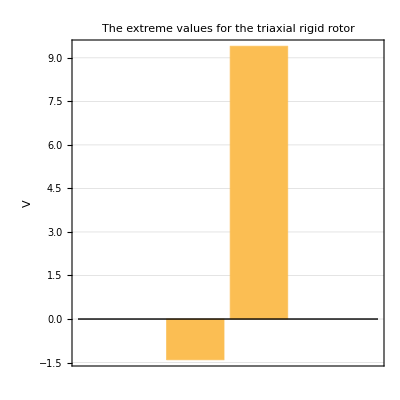

```mathematica
diff[spin_]:=BarChart[{MINMAX[spin][[1]],MINMAX[spin][[2]]},Frame->True,Axes->True,PlotTheme->"Detailed",FrameLabel->{"","V"},AspectRatio->1,PlotLabel->customize["The extreme values for \n the triaxial rigid rotor"]];
diff[12.5]
```